## Plot of EWS for Normal form Hopf

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/generic_models/normal_forms"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,30,10,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
bl=-1;
bh=0.2; (* realisation nuber for individual trajectory and power spectrum evolution *)
relNum=1;
rw=0.25; (* rolling window *)
```

## Import Data

```mathematica
ewsSingles=Import["data_export/hopf_ews_1/ews_singles.csv"];
specData=Import["data_export/hopf_ews_1/pspecs.csv"];
```

```mathematica
tmax=Max[ewsSingles[[2;;,3]]];
dt2=ewsSingles[[3,3]]-ewsSingles[[2,3]];
windowComps=rw*tmax/dt2-1;
```

## Trajectory Plots

```mathematica
(* columns *)
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax}

```mathematica
ewsSingles[[-1,3]]
```

399.

```mathematica
xSeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"x",_,_}][[;;,{3,4}]];
ySeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"y",_,_}][[;;,{3,4}]];
```

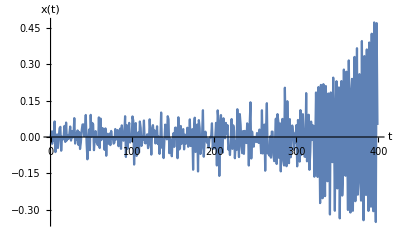

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[xSeries,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All},
ImagePadding->padTop]
```

## Hopf Bifurcation Diagram

### Specifications

```mathematica
(* Import data *)
rawdata=Import["bifurcation_data/hopf.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of mu *)
μbifVals=fulldata[[;;,1]];
tbifVals=(μbifVals-bl)*tmax /(bh-bl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections[[3]]=Cases[nodeSections[[3]],{x_,_,_,_}/; x>0] ; 
nodeSections=Append[nodeSections,Cases[nodeSections[[6]],{_,x_,_,_}/;x>0]];
nodeSections[[6]]=Cases[nodeSections[[6]],{_,x_,_,_}/;x<0]; (* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1,4,3,3}

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4,5,6,7}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{-1,1}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
];
```

### Output

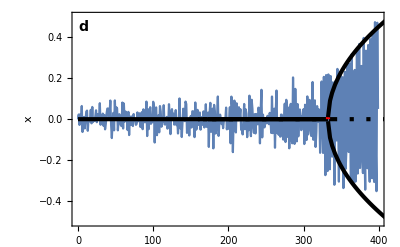

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.3;

figBifTrajHopf=Show[{plotX,bifPlotNormal},
PlotRange->{{0,tmax},{-0.5,0.5}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["d",14,Bold],Scaled[{0.035,0.93}]]}
]
```

## Single EWS Plots

### Variance

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,8}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
plotVar=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.5}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-1),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-1",14],indexPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

ListLinePlot::lpn: {{{0.,},{1.,},{2.,},{3.,},{4.,},{5.,},{6.,},{7.,},{8.,},{9.,},{10.,},{11.,},{12.,},{13.,},{14.,},{15.,},{16.,},{17.,},{18.,},{19.,},{20.,},{21.,},«8»,{30.,},{31.,},{32.,},{33.,},{34.,},{35.,},{36.,},{37.,},{38.,},{39.,},{40.,},{41.,},{42.,},{43.,},{44.,},{45.,},{46.,},{47.,},{48.,},{49.,},«350»},«3»,{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[{{{0.,},{1.,},{2.,},{3.,},{4.,},{5.,},{6.,},{7.,},{8.,},{9.,},{10.,},{11.,},{12.,},{13.,},{14.,},{15.,},{16.,},{17.,},{18.,},{19.,},{20.,},{21.,},{22.,},{23.,},{24.,},{25.,},{26.,},{27.,},{28.,},{29.,},{30.,},{31.,},{32.,},{33.,},{34.,},{35.,},{36.,},{37.,},{38.,},{39.,},{40.,},{41.,},{42.,},{43.,},{44.,},{45.,},{46.,},{47.,},{48.,},{49.,},{50.,},{51.,},{52.,},{53.,},{54.,},{55.,},{56.,},{57.,},{58.,},{59.,},{60.,},{61.,},{62.,},{63.,},{64.,},{65.,},{66.,},{67.,},{68.,},{69.,},{70.,},{71.,},{72.,},{73.,},{74.,},{75.,},{76.,},{77.,},{78.,},{79.,},{80.,},{81.,},{82.,},{83.,},{84.,},{85.,},{86.,},{87.,},{88.,},{89.,},{90.,},{91.,},{92.,},{93.,},{94.,},{95.,},{96.,},{97.,},{98.,},{99.,0.00153237},{100.,0.0016007},{101.,0.00163947},{102.,0.00176428},{103.,0.00178307},{104.,0.00180854},{105.,0.0018396},{106.,0.00179868},{107.,0.00180072},{108.,0.00184413},{109.,0.00185666},{110.,0.00186794},{111.,0.0018747},{112.,0.00186173},{113.,0.00182383},{114.,0.00186719},{115.,0.00187135},{116.,0.00187934},{117.,0.00186401},{118.,0.00185766},{119.,0.00185159},{120.,0.00185741},{121.,0.0019097},{122.,0.00190867},{123.,0.00196287},{124.,0.00195939},{125.,0.00197856},{126.,0.00197505},{127.,0.00198123},{128.,0.00198869},{129.,0.00193644},{130.,0.00194512},{131.,0.0019527},{132.,0.00194929},{133.,0.001993},{134.,0.00198052},{135.,0.0020819},{136.,0.00207047},{137.,0.00206233},{138.,0.00213362},{139.,0.00211346},{140.,0.00211888},{141.,0.00212018},{142.,0.0021166},{143.,0.00211923},{144.,0.00216697},{145.,0.00211426},{146.,0.00211116},{147.,0.00210807},{148.,0.00213352},{149.,0.00205912},{150.,0.00206237},{151.,0.00204744},{152.,0.00204059},{153.,0.00202428},{154.,0.00202318},{155.,0.00209056},{156.,0.00215864},{157.,0.0021709},{158.,0.00217532},{159.,0.00213932},{160.,0.00212084},{161.,0.00207703},{162.,0.00208742},{163.,0.00209875},{164.,0.00209032},{165.,0.00209483},{166.,0.00206449},{167.,0.00207188},{168.,0.00201983},{169.,0.002022},{170.,0.00208031},{171.,0.0020816},{172.,0.00209087},{173.,0.0020898},{174.,0.00225857},{175.,0.00226865},{176.,0.00233871},{177.,0.00236326},{178.,0.00237534},{179.,0.00239637},{180.,0.00258899},{181.,0.00264308},{182.,0.00265271},{183.,0.00268048},{184.,0.00270065},{185.,0.00269382},{186.,0.00279696},{187.,0.00283896},{188.,0.00284166},{189.,0.00284496},{190.,0.00284428},{191.,0.00277788},{192.,0.00270647},{193.,0.00270047},{194.,0.00267523},{195.,0.00266878},{196.,0.00263604},{197.,0.00266743},{198.,0.00268835},{199.,0.00268563},{200.,0.00263199},{201.,0.00258592},{202.,0.00249594},{203.,0.00259952},{204.,0.00269989},{205.,0.00268937},{206.,0.00293065},{207.,0.00292976},{208.,0.00297858},{209.,0.00295346},{210.,0.00297451},{211.,0.00302926},{212.,0.00303653},{213.,0.00303529},{214.,0.0030275},{215.,0.00302431},{216.,0.00304405},{217.,0.00306788},{218.,0.00307855},{219.,0.00310748},{220.,0.00309844},{221.,0.00310543},{222.,0.00312446},{223.,0.00309838},{224.,0.00309574},{225.,0.00314209},{226.,0.00314373},{227.,0.00315912},{228.,0.00329643},{229.,0.00329649},{230.,0.00333672},{231.,0.00342856},{232.,0.00345731},{233.,0.00342181},{234.,0.00346037},{235.,0.00336261},{236.,0.00338708},{237.,0.00339584},{238.,0.00332311},{239.,0.00332612},{240.,0.00333486},{241.,0.00334849},{242.,0.00347805},{243.,0.00342711},{244.,0.00358961},{245.,0.00361894},{246.,0.00362606},{247.,0.00362508},{248.,0.00357767},{249.,0.00357671},{250.,0.00357396},{251.,0.00356164},{252.,0.00354974},{253.,0.00353388},{254.,0.0035378},{255.,0.00347697},{256.,0.00340652},{257.,0.00342174},{258.,0.0035335},{259.,0.00355265},{260.,0.00355041},{261.,0.00357255},{262.,0.00374276},{263.,0.00373361},{264.,0.00393951},{265.,0.00397465},{266.,0.00398714},{267.,0.0040224},{268.,0.00400901},{269.,0.00407056},{270.,0.00401907},{271.,0.00401545},{272.,0.00405351},{273.,0.00412799},{274.,0.00395661},{275.,0.00401181},{276.,0.00405235},{277.,0.00412149},{278.,0.00414967},{279.,0.00418398},{280.,0.00402898},{281.,0.00416203},{282.,0.00417371},{283.,0.00419511},{284.,0.00426285},{285.,0.0043845},{286.,0.00469215},{287.,0.0046317},{288.,0.0047633},{289.,0.00499155},{290.,0.0049923},{291.,0.00509587},{292.,0.00515787},{293.,0.00520496},{294.,0.00520593},{295.,0.0052324},{296.,0.00523984},{297.,0.00522826},{298.,0.00521045},{299.,0.00521368},{300.,0.00522158},{301.,0.00536129},{302.,0.00537831},{303.,0.00525882},{304.,0.00522777},{305.,0.00531017},{306.,0.00511147},{307.,0.00512634},{308.,0.00513319},{309.,0.00511929},{310.,0.0051423},{311.,0.00513856},{312.,0.00547425},{313.,0.00556977},{314.,0.00554086},{315.,0.00563001},{316.,0.00577403},{317.,0.0057873},{318.,0.00582399},{319.,0.00577578},{320.,0.00580272},{321.,0.00576474},{322.,0.00600314},{323.,0.00598762},{324.,0.00633461},{325.,0.00626519},{326.,0.00652513},{327.,0.00694202},{328.,0.0068293},{329.,0.00755881},{330.,0.00797835},{331.,0.0079039},{332.,0.00849588},{333.,0.00898319},{334.,},{335.,},{336.,},{337.,},{338.,},{339.,},{340.,},{341.,},{342.,},{343.,},{344.,},{345.,},{346.,},{347.,},{348.,},{349.,},{350.,},{351.,},{352.,},{353.,},{354.,},{355.,},{356.,},{357.,},{358.,},{359.,},{360.,},{361.,},{362.,},{363.,},{364.,},{365.,},{366.,},{367.,},{368.,},{369.,},{370.,},{371.,},{372.,},{373.,},{374.,},{375.,},{376.,},{377.,},{378.,},{379.,},{380.,},{381.,},{382.,},{383.,},{384.,},{385.,},{386.,},{387.,},{388.,},{389.,},{390.,},{391.,},{392.,},{393.,},{394.,},{395.,},{396.,},{397.,},{398.,},{399.,}},{},{},{},{}},Joined→True,LabelStyle→14,Frame→True,PlotRange→{{0,399.},{0,0.5}},PlotStyle→RGBColor[0.368417, 0.506779, 0.709798],FrameLabel→{{Var,},{,}},FrameTicksStyle→{{Automatic,Automatic},{Directive[FontOpacity→0,FontSize→0],Automatic}},FrameTicks→{{{{0,0},{1/5,2},{2/5,4},{3/5,6},{4/5,8},{1,10}},Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{10,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[×10^-1,Scaled[{0.065,1.11}]],Text[b,Scaled[{0.035,0.86}]]}]

### Autocorrelation combined

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,9,10,11}]],
{_,"x",_,_,_,_}]⟦;;,{3,i}⟧,
{i,{4,5,6}}];
```

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],Table["τ="<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.1}]
```

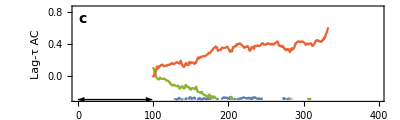

```mathematica
ymin=-1;
ymax=1;
plotLagnAC=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->TMBcolours[[{1,3,4}]],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Smax

```mathematica
Position[ewsSingles[[1]],"Smax"][[1,1]]
```

22

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,22}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
plotSmax=ListPlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.06}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{10^(-2)*Range[0,10,2],Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-2",14],indexPos],
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

ListPlot::lpn: {{{99.,0.000149678},{119.,0.000171812},{139.,0.000170287},{159.,0.000168897},{179.,0.000232786},{199.,0.000304396},{219.,0.000349281},{239.,0.000359845},{259.,0.000500119},{279.,0.000458846},{299.,0.000718012},{319.,0.000826137}},{},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{{99.,0.000149678},{119.,0.000171812},{139.,0.000170287},{159.,0.000168897},{179.,0.000232786},{199.,0.000304396},{219.,0.000349281},{239.,0.000359845},{259.,0.000500119},{279.,0.000458846},{299.,0.000718012},{319.,0.000826137}},{},{},{},{}},Joined→True,LabelStyle→14,Frame→True,PlotRange→{{0,399.},{0,0.06}},PlotStyle→RGBColor[0.368417, 0.506779, 0.709798],FrameLabel→{{S_max,},{,}},FrameTicksStyle→{{Automatic,Automatic},{Directive[FontOpacity→0,FontSize→0],Automatic}},FrameTicks→{{{{0,0},{1/50,2},{1/25,4},{3/50,6},{2/25,8},{1/10,10}},Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{10,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[×10^-2,Scaled[{0.065,1.11}]],Text[e,Scaled[{0.035,0.86}]]}]

### AIC

```mathematica
Position[ewsSingles[[1]],"AIC null"][[1,1]]
```

17

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],{"ω_fold","ω_hopf","ω_null"},Spacings->{0,0.1}]
```

```mathematica
seriesFold=Table[
Cases[
ewsSingles[[relNum;;,{1,2,3,15}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
seriesHopf=Table[
Cases[
ewsSingles[[relNum;;,{1,2,3,16}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
seriesNull=Table[
Cases[
ewsSingles[[relNum;;,{1,2,3,17}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
plotAIC=ListLinePlot[Join[seriesFold,seriesHopf,seriesNull],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
PlotStyle->TMBcolours[[{1,1,1,1,1,3,3,3,3,3,4,4,4,4,4}]],
PlotLegends->Placed[legend,{0.15,0.72}],
Frame->True,
FrameLabel->{{"AIC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

ListLinePlot::lpn: {{{99.,8.60238×10^-11},{119.,2.8302×10^-8},{139.,5.50694×10^-13},{159.,4.23149×10^-17},{179.,4.91796×10^-17},{199.,5.51072×10^-24},{219.,2.91865×10^-28},{239.,4.63461×10^-22},{259.,2.45958×10^-24},{279.,3.77285×10^-24},{299.,7.64511×10^-18},{319.,6.8767×10^-29}},{},{},{},{},«6»,{},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[{{{99.,8.60238×10^-11},{119.,2.8302×10^-8},{139.,5.50694×10^-13},{159.,4.23149×10^-17},{179.,4.91796×10^-17},{199.,5.51072×10^-24},{219.,2.91865×10^-28},{239.,4.63461×10^-22},{259.,2.45958×10^-24},{279.,3.77285×10^-24},{299.,7.64511×10^-18},{319.,6.8767×10^-29}},{},{},{},{},{{99.,0.999998},{119.,0.999659},{139.,1.},{159.,1.},{179.,1.},{199.,1.},{219.,1.},{239.,1.},{259.,1.},{279.,1.},{299.,1.},{319.,1.}},{},{},{},{},{{99.,1.64005×10^-6},{119.,0.000340958},{139.,4.3413×10^-9},{159.,2.86398×10^-14},{179.,1.48422×10^-14},{199.,7.32864×10^-22},{219.,3.28787×10^-26},{239.,6.09282×10^-20},{259.,2.22243×10^-22},{279.,5.8325×10^-22},{299.,6.20328×10^-16},{319.,8.31557×10^-27}},{},{},{},{}},Joined→True,LabelStyle→14,PlotRange→{{0,399.},{-0.05,1.05}},PlotStyle→{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179]},PlotLegends→Placed[,{0.15,0.72}],Frame→True,FrameLabel→{{AIC,},{Time,}},FrameTicksStyle→{{Automatic,Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{40,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[f,Scaled[{0.035,0.86}]]}]

### Power Spectrum

```mathematica
specData//Dimensions
```

{985,5}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,3]]]
```

{99.,119.,139.,159.,179.,199.,219.,239.,259.,279.,299.,319.}

```mathematica
pspecs=Table[
Cases[specData,
{relNum,"x",i,_,_}]⟦;;,{4,5}⟧,
{i,plotTimes}];
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

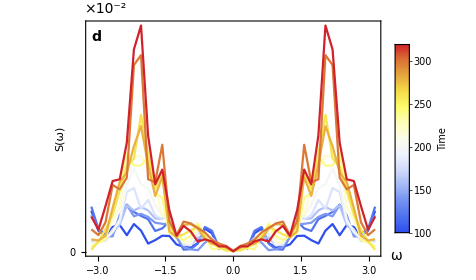

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
plotPspec=ListLinePlot[pspecs,
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{2*padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-2",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,20,2]*10^(-2),Range[0,20,2]}],None},{Automatic,None}},
PlotLegends->Placed[colLegend,Scaled[{0.91,0.58}]]]
```

## Grid: Single EWS

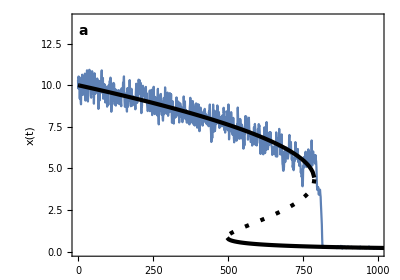
-Graphics- | -Graphics-
ListLinePlot[{{{0.,},{1.,},{2.,},{3.,},{4.,},{5.,},{6.,},{7.,},{8.,},{9.,},{10.,},{11.,},{12.,},{13.,},{14.,},{15.,},{16.,},{17.,},{18.,},{19.,},{20.,},{21.,},{22.,},{23.,},{24.,},{25.,},{26.,},{27.,},{28.,},{29.,},{30.,},{31.,},{32.,},{33.,},{34.,},{35.,},{36.,},{37.,},{38.,},{39.,},{40.,},{41.,},{42.,},{43.,},{44.,},{45.,},{46.,},{47.,},{48.,},{49.,},{50.,},{51.,},{52.,},{53.,},{54.,},{55.,},{56.,},{57.,},{58.,},{59.,},{60.,},{61.,},{62.,},{63.,},{64.,},{65.,},{66.,},{67.,},{68.,},{69.,},{70.,},{71.,},{72.,},{73.,},{74.,},{75.,},{76.,},{77.,},{78.,},{79.,},{80.,},{81.,},{82.,},{83.,},{84.,},{85.,},{86.,},{87.,},{88.,},{89.,},{90.,},{91.,},{92.,},{93.,},{94.,},{95.,},{96.,},{97.,},{98.,},{99.,0.00153237},{100.,0.0016007},{101.,0.00163947},{102.,0.00176428},{103.,0.00178307},{104.,0.00180854},{105.,0.0018396},{106.,0.00179868},{107.,0.00180072},{108.,0.00184413},{109.,0.00185666},{110.,0.00186794},{111.,0.0018747},{112.,0.00186173},{113.,0.00182383},{114.,0.00186719},{115.,0.00187135},{116.,0.00187934},{117.,0.00186401},{118.,0.00185766},{119.,0.00185159},{120.,0.00185741},{121.,0.0019097},{122.,0.00190867},{123.,0.00196287},{124.,0.00195939},{125.,0.00197856},{126.,0.00197505},{127.,0.00198123},{128.,0.00198869},{129.,0.00193644},{130.,0.00194512},{131.,0.0019527},{132.,0.00194929},{133.,0.001993},{134.,0.00198052},{135.,0.0020819},{136.,0.00207047},{137.,0.00206233},{138.,0.00213362},{139.,0.00211346},{140.,0.00211888},{141.,0.00212018},{142.,0.0021166},{143.,0.00211923},{144.,0.00216697},{145.,0.00211426},{146.,0.00211116},{147.,0.00210807},{148.,0.00213352},{149.,0.00205912},{150.,0.00206237},{151.,0.00204744},{152.,0.00204059},{153.,0.00202428},{154.,0.00202318},{155.,0.00209056},{156.,0.00215864},{157.,0.0021709},{158.,0.00217532},{159.,0.00213932},{160.,0.00212084},{161.,0.00207703},{162.,0.00208742},{163.,0.00209875},{164.,0.00209032},{165.,0.00209483},{166.,0.00206449},{167.,0.00207188},{168.,0.00201983},{169.,0.002022},{170.,0.00208031},{171.,0.0020816},{172.,0.00209087},{173.,0.0020898},{174.,0.00225857},{175.,0.00226865},{176.,0.00233871},{177.,0.00236326},{178.,0.00237534},{179.,0.00239637},{180.,0.00258899},{181.,0.00264308},{182.,0.00265271},{183.,0.00268048},{184.,0.00270065},{185.,0.00269382},{186.,0.00279696},{187.,0.00283896},{188.,0.00284166},{189.,0.00284496},{190.,0.00284428},{191.,0.00277788},{192.,0.00270647},{193.,0.00270047},{194.,0.00267523},{195.,0.00266878},{196.,0.00263604},{197.,0.00266743},{198.,0.00268835},{199.,0.00268563},{200.,0.00263199},{201.,0.00258592},{202.,0.00249594},{203.,0.00259952},{204.,0.00269989},{205.,0.00268937},{206.,0.00293065},{207.,0.00292976},{208.,0.00297858},{209.,0.00295346},{210.,0.00297451},{211.,0.00302926},{212.,0.00303653},{213.,0.00303529},{214.,0.0030275},{215.,0.00302431},{216.,0.00304405},{217.,0.00306788},{218.,0.00307855},{219.,0.00310748},{220.,0.00309844},{221.,0.00310543},{222.,0.00312446},{223.,0.00309838},{224.,0.00309574},{225.,0.00314209},{226.,0.00314373},{227.,0.00315912},{228.,0.00329643},{229.,0.00329649},{230.,0.00333672},{231.,0.00342856},{232.,0.00345731},{233.,0.00342181},{234.,0.00346037},{235.,0.00336261},{236.,0.00338708},{237.,0.00339584},{238.,0.00332311},{239.,0.00332612},{240.,0.00333486},{241.,0.00334849},{242.,0.00347805},{243.,0.00342711},{244.,0.00358961},{245.,0.00361894},{246.,0.00362606},{247.,0.00362508},{248.,0.00357767},{249.,0.00357671},{250.,0.00357396},{251.,0.00356164},{252.,0.00354974},{253.,0.00353388},{254.,0.0035378},{255.,0.00347697},{256.,0.00340652},{257.,0.00342174},{258.,0.0035335},{259.,0.00355265},{260.,0.00355041},{261.,0.00357255},{262.,0.00374276},{263.,0.00373361},{264.,0.00393951},{265.,0.00397465},{266.,0.00398714},{267.,0.0040224},{268.,0.00400901},{269.,0.00407056},{270.,0.00401907},{271.,0.00401545},{272.,0.00405351},{273.,0.00412799},{274.,0.00395661},{275.,0.00401181},{276.,0.00405235},{277.,0.00412149},{278.,0.00414967},{279.,0.00418398},{280.,0.00402898},{281.,0.00416203},{282.,0.00417371},{283.,0.00419511},{284.,0.00426285},{285.,0.0043845},{286.,0.00469215},{287.,0.0046317},{288.,0.0047633},{289.,0.00499155},{290.,0.0049923},{291.,0.00509587},{292.,0.00515787},{293.,0.00520496},{294.,0.00520593},{295.,0.0052324},{296.,0.00523984},{297.,0.00522826},{298.,0.00521045},{299.,0.00521368},{300.,0.00522158},{301.,0.00536129},{302.,0.00537831},{303.,0.00525882},{304.,0.00522777},{305.,0.00531017},{306.,0.00511147},{307.,0.00512634},{308.,0.00513319},{309.,0.00511929},{310.,0.0051423},{311.,0.00513856},{312.,0.00547425},{313.,0.00556977},{314.,0.00554086},{315.,0.00563001},{316.,0.00577403},{317.,0.0057873},{318.,0.00582399},{319.,0.00577578},{320.,0.00580272},{321.,0.00576474},{322.,0.00600314},{323.,0.00598762},{324.,0.00633461},{325.,0.00626519},{326.,0.00652513},{327.,0.00694202},{328.,0.0068293},{329.,0.00755881},{330.,0.00797835},{331.,0.0079039},{332.,0.00849588},{333.,0.00898319},{334.,},{335.,},{336.,},{337.,},{338.,},{339.,},{340.,},{341.,},{342.,},{343.,},{344.,},{345.,},{346.,},{347.,},{348.,},{349.,},{350.,},{351.,},{352.,},{353.,},{354.,},{355.,},{356.,},{357.,},{358.,},{359.,},{360.,},{361.,},{362.,},{363.,},{364.,},{365.,},{366.,},{367.,},{368.,},{369.,},{370.,},{371.,},{372.,},{373.,},{374.,},{375.,},{376.,},{377.,},{378.,},{379.,},{380.,},{381.,},{382.,},{383.,},{384.,},{385.,},{386.,},{387.,},{388.,},{389.,},{390.,},{391.,},{392.,},{393.,},{394.,},{395.,},{396.,},{397.,},{398.,},{399.,}},{},{},{},{}},Joined→True,LabelStyle→14,Frame→True,PlotRange→{{0,399.},{0,0.5}},PlotStyle→RGBColor[0.368417, 0.506779, 0.709798],FrameLabel→{{Var,},{,}},FrameTicksStyle→{{Automatic,Automatic},{Directive[FontOpacity→0,FontSize→0],Automatic}},FrameTicks→{{{{0,0},{1/5,2},{2/5,4},{3/5,6},{4/5,8},{1,10}},Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{10,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[×10^-1,Scaled[{0.065,1.11}]],Text[b,Scaled[{0.035,0.86}]]}] | ListPlot[{{{99.,0.000149678},{119.,0.000171812},{139.,0.000170287},{159.,0.000168897},{179.,0.000232786},{199.,0.000304396},{219.,0.000349281},{239.,0.000359845},{259.,0.000500119},{279.,0.000458846},{299.,0.000718012},{319.,0.000826137}},{},{},{},{}},Joined→True,LabelStyle→14,Frame→True,PlotRange→{{0,399.},{0,0.06}},PlotStyle→RGBColor[0.368417, 0.506779, 0.709798],FrameLabel→{{S_max,},{,}},FrameTicksStyle→{{Automatic,Automatic},{Directive[FontOpacity→0,FontSize→0],Automatic}},FrameTicks→{{{{0,0},{1/50,2},{1/25,4},{3/50,6},{2/25,8},{1/10,10}},Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{10,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[×10^-2,Scaled[{0.065,1.11}]],Text[e,Scaled[{0.035,0.86}]]}]
-Graphics- | ListLinePlot[{{{99.,8.60238×10^-11},{119.,2.8302×10^-8},{139.,5.50694×10^-13},{159.,4.23149×10^-17},{179.,4.91796×10^-17},{199.,5.51072×10^-24},{219.,2.91865×10^-28},{239.,4.63461×10^-22},{259.,2.45958×10^-24},{279.,3.77285×10^-24},{299.,7.64511×10^-18},{319.,6.8767×10^-29}},{},{},{},{},{{99.,0.999998},{119.,0.999659},{139.,1.},{159.,1.},{179.,1.},{199.,1.},{219.,1.},{239.,1.},{259.,1.},{279.,1.},{299.,1.},{319.,1.}},{},{},{},{},{{99.,1.64005×10^-6},{119.,0.000340958},{139.,4.3413×10^-9},{159.,2.86398×10^-14},{179.,1.48422×10^-14},{199.,7.32864×10^-22},{219.,3.28787×10^-26},{239.,6.09282×10^-20},{259.,2.22243×10^-22},{279.,5.8325×10^-22},{299.,6.20328×10^-16},{319.,8.31557×10^-27}},{},{},{},{}},Joined→True,LabelStyle→14,PlotRange→{{0,399.},{-0.05,1.05}},PlotStyle→{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179]},PlotLegends→Placed[,{0.15,0.72}],Frame→True,FrameLabel→{{AIC,},{Time,}},FrameTicksStyle→{{Automatic,Automatic},{Automatic,Automatic}},PlotRangeClipping→False,ImagePadding→{{60,30},{40,20}},ImageSize→400,AspectRatio→0.3,Epilog→{Directive[{GrayLevel[0]}],Arrowheads[{-0.03,0.03}],Arrow[{Scaled[{0,0.15},{0,0}],Scaled[{0,0.15},{98.75,0}]}],Text[f,Scaled[{0.035,0.86}]]}]
 | 
 |

```mathematica
gridPlot=Grid[{{bifTrajX,plotPspec},{plotVar,plotSmax},{plotLagnAC,plotAIC},{},{}},Spacings->{-1.5,0}]
```

```mathematica
(*Export["figures/plot_ews_fold.png",gridPlot,ImageResolution->200];*)
```